```mathematica
s = 0.017;
ar = 0.86;
e = 0.9;
m = 0.003;
g = 9.8;
rho = 1.225;
cla = π ar /(1+Sqrt[1+(ar/2)^2]);
cdo = 0.02;
ϵ =1/(π e ar);
cl = Sqrt[cdo/ϵ];
cd = cdo + ϵ cl^2;
ldmax = cl/cd;
γo = -ArcTan[1/ldmax];
vo = Sqrt[2 m g/(rho s (cl Cos[γo]-cd Sin[γo]))];
α = cl/cla;
h = 2;
r = 0;
simt = 6;
q = 1/2rho v[t]^2;
eqn = {v'[t] == (-cd q s-m g Sin[γ[t]])/m, γ'[t]==(cl q s - m g Cos[γ[t]])/(m v[t]), y'[t] == v[t]Sin[γ[t]], x'[t]== Cos[γ[t]],x[0]== 0, y[0]== 2, v[0]== 2.5 vo,γ[0]== 0} ;
sol= NDSolve[eqn,{x[t],y[t],v[t],γ[t]},{t,0,simt}]
```

{{x[t]→InterpolatingFunction[{{0., 6.}}, <>][t],y[t]→InterpolatingFunction[{{0., 6.}}, <>][t],v[t]→InterpolatingFunction[{{0., 6.}}, <>][t],γ[t]→InterpolatingFunction[{{0., 6.}}, <>][t]}}

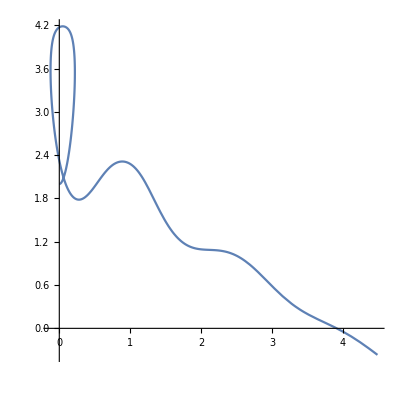

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,simt}]
```

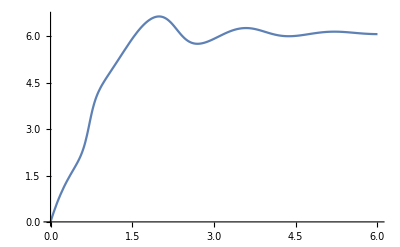

```mathematica
Plot[Evaluate[γ[t]/.sol],{t,0,simt},PlotRange->All]
```